```mathematica
imageset1VoxelVol= (Quantity[212.6, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"];
imageset2VoxelVol= (Quantity[236.16, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"];
imageset3VoxelVol= (Quantity[151.82, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"];
imageset4VoxelVol= (Quantity[163.5, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"];
imageset5VoxelVol=(Quantity[236.16, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"];
imageset6VoxelVol=(Quantity[236.16, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"];
imageset7VoxelVol=(Quantity[265.69, "Micrometers"]/1600)^2*Quantity[1, "Micrometers"];
```

```mathematica
orderFiles[dir_]:=Module[{filenames,order},
filenames=Import[dir];
order=Ordering@*Flatten@StringCases[filenames,x_~~y:DigitCharacter..~~".tif":> ToExpression@y];
filenames[[order]]
];
```

```mathematica
generateMesh[dir_String,voxelVol_]:=Module[{filenames,masks,im3d,morpComp,dim,dimtake,im3d2,mesh},
filenames=orderFiles[dir];
masks=Binarize@Import[dir<>#]&/@filenames;
im3d=Image3D@masks;
morpComp=MorphologicalComponents[im3d];
dim=First@ImageDimensions[im3d];
dimtake=MapAt[#-1&,
(MapAt[dim-#&,Reverse@Thread[Last@@ComponentMeasurements[morpComp,"BoundingBox"]],{2}]//Round)/. 0->1,{1,2}];
im3d2=Image3D[ImageTake[im3d,Sequence@@dimtake],BoxRatios->{1, 1, 1},ImageSize->Tiny];
Print[im3d2];
mesh=ImageMesh[im3d2,Method->"DualMarchingCubes",BoxRatios->{1, 1, 1},ImageSize->Tiny];
Print[{#,voxelVol*Abs@Volume[#]}&@mesh];
Print[{#,voxelVol*Abs[Volume[#]]}&@ImageMesh[GaussianFilter[im3d2,3],Method-> "DualMarchingCubes",BoxRatios->{1, 1, 1},ImageSize->Tiny]];
];
```

```mathematica
fitEllipsoid3D[image_Image3D]:=Block[{im,pixpos,meanpos,convexHull,mesh,points,minval,rules,ainv,centre,Σ,ellipsoidLJ,U,λ,U2},
im=image;
pixpos=PixelValuePositions[im,1];
meanpos=N@Mean[pixpos];
convexHull=ConvexHullMesh[#-meanpos&/@pixpos,BoxRatios->{1, 1, 1}];Print[mesh=DiscretizeRegion[convexHull,BoxRatios->{1, 1, 1},ImageSize->Tiny]];
points=MeshPrimitives[mesh,0]/.Point->Sequence;
 {minval,rules}=NMinimize[{-Log[Det[a]],{a(\[VectorGreaterEqual])_ 0, Table[Norm[a.xi+b]≤1, {xi,points}]}}, {a,b∈Vectors[3]}];
ainv=Inverse[a/.rules];
centre=-ainv.(b/.rules);
Σ=ainv.ainv;
ellipsoidLJ=Ellipsoid[centre,Σ];
Print@Graphics3D[{PointSize[0.01],Black,Point[points],Opacity[.2],Blue,ellipsoidLJ},
Axes->True,BoxRatios->{1,1,1},ImageSize->Medium];
{U,λ,U2}=SingularValueDecomposition[Σ];
{Sqrt@Diagonal[λ],Sqrt@Eigensystem[Σ][[1]]}
];
```

```mathematica
fitEllipsoid3DAlt[image_Image3D]:=Block[{im,pixpos,meanpos,convexHull,mesh,points,minval,rules,ainv,centre,Σ,ellipsoidLJ,U,λ,U2},
im=image;
pixpos=PixelValuePositions[MorphologicalPerimeter@im,1];
meanpos=N@Mean[pixpos];
points=#-meanpos&/@pixpos;
 {minval,rules}=NMinimize[{-Log[Det[a]],{a(\[VectorGreaterEqual])_ 0, Table[Norm[a.xi+b]≤1, {xi,points}]}}, {a,b∈Vectors[3]}];
ainv=Inverse[a/.rules];
centre=-ainv.(b/.rules);
Σ=ainv.ainv;
ellipsoidLJ=Ellipsoid[centre,Σ];
Print@Graphics3D[{PointSize[0.01],Black,Point[points],Opacity[.2],Blue,ellipsoidLJ},
Axes->True,BoxRatios->{1,1,1},ImageSize->Medium];
{U,λ,U2}=SingularValueDecomposition[Σ];
{Sqrt@Diagonal[λ],Sqrt@Eigensystem[Σ][[1]]}
];
```

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@3D cell shape classifier\\96 hrs\\";
```

## E-cadherin expressing cells (96 hrs)

### cell-1

```mathematica
generateMesh[dir<>"image set 1\\ecad cells\\cell-1\\",imageset1VoxelVol]
```

-Graphics3D-

{-Graphics3D-,967.412 µm^3}

{-Graphics3D-,969.457 µm^3}

### cell-2

```mathematica
generateMesh[dir<>"image set 1\\ecad cells\\cell-2\\",imageset1VoxelVol]
```

-Graphics3D-

{-Graphics3D-,1138.57 µm^3}

{-Graphics3D-,1134.83 µm^3}

### cell-3

```mathematica
generateMesh[dir<>"image set 1\\ecad cells\\cell-3\\",imageset1VoxelVol]
```

-Graphics3D-

{-Graphics3D-,899.382 µm^3}

{-Graphics3D-,895.08 µm^3}

### cell-4

```mathematica
generateMesh[dir<>"image set 1\\ecad cells\\cell-4\\",imageset1VoxelVol]
```

-Graphics3D-

{-Graphics3D-,1083.17 µm^3}

{-Graphics3D-,1072.18 µm^3}

### cell-5

```mathematica
generateMesh[dir<>"image set 1\\ecad cells\\cell-5\\",imageset1VoxelVol]
```

-Graphics3D-

{-Graphics3D-,961.814 µm^3}

{-Graphics3D-,956. µm^3}

### cell-6

```mathematica
generateMesh[dir<>"image set 1\\ecad cells\\cell-6\\",imageset1VoxelVol]
```

-Graphics3D-

{-Graphics3D-,964.954 µm^3}

{-Graphics3D-,953.644 µm^3}

### cell-7

```mathematica
generateMesh[dir<>"image set 1\\ecad cells\\cell-7\\",imageset1VoxelVol]
```

-Graphics3D-

{-Graphics3D-,837.087 µm^3}

{-Graphics3D-,829.98 µm^3}

### cell-8

```mathematica
generateMesh[dir<>"image set 4\\ecad cells\\cell-8\\",imageset4VoxelVol]
```

-Graphics3D-

{-Graphics3D-,1381.31 µm^3}

{-Graphics3D-,1374. µm^3}

### cell-9

```mathematica
generateMesh[dir<>"image set 5\\ecad cells\\cell-9\\",imageset5VoxelVol]
```

-Graphics3D-

{-Graphics3D-,1274.41 µm^3}

{-Graphics3D-,1251.86 µm^3}

## Neighbouring cells (96 hrs)

### cell-1

```mathematica
generateMesh[dir<>"image set 1\\brachyury cells\\cell-1\\",imageset1VoxelVol]
```

-Graphics3D-

{-Graphics3D-,296.449 µm^3}

{-Graphics3D-,311.104 µm^3}

### cell-2

```mathematica
generateMesh[dir<>"image set 2\\brachyury cells\\cell-2\\",imageset2VoxelVol]
```

-Graphics3D-

{-Graphics3D-,343.744 µm^3}

{-Graphics3D-,336.419 µm^3}

### cell-3

```mathematica
generateMesh[dir<>"image set 3\\brachyury cells\\cell-3\\",imageset3VoxelVol]
```

-Graphics3D-

{-Graphics3D-,255.425 µm^3}

{-Graphics3D-,256.71 µm^3}

### cell-4

```mathematica
generateMesh[dir<>"image set 4\\brachyury cells\\cell-4\\",imageset4VoxelVol]
```

-Graphics3D-

{-Graphics3D-,226.056 µm^3}

{-Graphics3D-,242.151 µm^3}

### cell-5

```mathematica
generateMesh[dir<>"image set 5\\brachyury cells\\cell-5\\",imageset5VoxelVol]
```

-Graphics3D-

{-Graphics3D-,244.039 µm^3}

{-Graphics3D-,247.692 µm^3}

### cell-6

```mathematica
generateMesh[dir<>"image set 6\\brachyury cells\\cell-6\\",imageset6VoxelVol]
```

-Graphics3D-

{-Graphics3D-,278.94 µm^3}

{-Graphics3D-,299.613 µm^3}

### cell-7

```mathematica
generateMesh[dir<>"image set 6\\brachyury cells\\cell-7\\",imageset6VoxelVol]
```

-Graphics3D-

{-Graphics3D-,311.751 µm^3}

{-Graphics3D-,307.927 µm^3}

## cluster analysis

```mathematica
brachImages={-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-};
ecadImages={-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-};
```

```mathematica
FeatureSpacePlot3D[RandomSample@Join[Style[Callout[#,"Ecad",Background->None],Red]&/@ecadImages,Style[Callout[#,"Brach",Background->None],Blue]&/@brachImages],Method->"PrincipalComponentsAnalysis",PlotStyle->Directive[Opacity[0.3],PointSize[0.028]],ImageSize->Large,Boxed->True]
```

-Graphics3D-

```mathematica
volumeEcad={Quantity[969.4581653236208, ("Micrometers")^3],Quantity[1134.8348700342035, ("Micrometers")^3],Quantity[895.0803849599641, ("Micrometers")^3],Quantity[1072.1794343900242, ("Micrometers")^3],Quantity[956.0003478352069, ("Micrometers")^3],Quantity[953.6444227217423, ("Micrometers")^3],Quantity[829.9819519822719, ("Micrometers")^3],Quantity[1373.9979242686177, ("Micrometers")^3],Quantity[1251.855005629671, ("Micrometers")^3]};
volumeBrach={Quantity[311.1027867587147, ("Micrometers")^3],Quantity[336.41855603783534, ("Micrometers")^3],Quantity[256.70987175759495, ("Micrometers")^3],Quantity[242.15118784116666, ("Micrometers")^3],Quantity[247.69186022570162, ("Micrometers")^3],Quantity[299.6130660016753, ("Micrometers")^3],Quantity[307.92701955814965, ("Micrometers")^3]};
```

```mathematica
volclusters=FindClusters[volumeBrach~Join~volumeEcad,2];
```

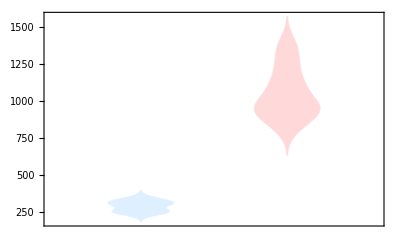

```mathematica
DistributionChart[volclusters,ChartStyle->{LightBlue,LightRed}]
```

```mathematica
Style[#2/#&@@Mean/@volclusters,Bold,LightPurple,40,FontFamily->"Arial Baltic"]
```

3.667

## Minimal Ellipsoidal Fit (Conic Optimization)

```mathematica
SeedRandom[1];
n=3;
points=RandomPoint[Ball[],5000];
```

```mathematica
{minval,rules}=NMinimize[{-Log[Det[a]],{a(\[VectorGreaterEqual])_ 0, Table[Norm[a.xi+b]≤1, {xi,points}]}}, {a,b∈Vectors[n]}]
```

{-0.00235442,{a→{{0.999486,-0.000628021,-0.000618221},{-0.000628021,1.00056,0.000193685},{-0.000618221,0.000193685,1.00231}},b→{0.000643215,-0.000410424,0.0000827028}}}

```mathematica
ainv=Inverse[a/.rules];
centre=-ainv.(b/.rules);
Σ=ainv.ainv;
RegionMeasure[ellipsoidLJ=Ellipsoid[centre,Σ]]
```

4.17894

```mathematica
Graphics3D[{PointSize[0.01],Point[points],Opacity[.25],Green,ellipsoidLJ},BoxRatios->{1,1,1},ImageSize->Small]
```

-Graphics3D-

```mathematica
(*almost a minimal bounding sphere*)
```

```mathematica
{U,λ,U2}=SingularValueDecomposition[Σ];
{Sqrt@Diagonal[λ],Sqrt@*First@Eigensystem[Σ]}
```

{{1.00088,0.999259,0.997512},{1.00088,0.999259,0.997512}}

```mathematica
(*rotation matrix for aligning ellipsoid with x-axis *)
```

```mathematica
rot=Det[U]Transpose[U];
w=NullSpace[rot-IdentityMatrix[3]][[1]];
V=RotationMatrix[{{1,0,0},w}];
θ=-ArcTan@@(Transpose[V].rot.V)[[2,2;;3]];
Max[Abs[RotationMatrix[θ,w]-rot]]
```

2.22045×10^-16

```mathematica
Show[Graphics3D[{Opacity[0.5],Red,ellipsoidLJ,Blue,Rotate[#,θ,w,centre]&@ellipsoidLJ},Lighting->"Neutral"],Axes-> True,ImageSize->Small]
```

-Graphics3D-

## Fitting ellipsoids to cells

```mathematica
n=3;
```

```mathematica
im=ecadImages[[1]];
pixpos=PixelValuePositions[im,1];
meanpos=N@Mean[pixpos];
convexHull=ConvexHullMesh[#-meanpos&/@pixpos,BoxRatios->{1, 1, 1}];
mesh=DiscretizeRegion[convexHull,BoxRatios->{1, 1, 1},ImageSize->Tiny]
data=MeshPrimitives[mesh,0]/.Point->Sequence;
points=data;
 {minval,rules}=NMinimize[{-Log[Det[a]],{a(\[VectorGreaterEqual])_ 0, Table[Norm[a.xi+b]≤1, {xi,points}]}}, {a,b∈Vectors[n]}]
```

-Graphics3D-

{10.2479,{a→{{0.0139635,-0.000500023,0.00090161},{-0.000500023,0.0160473,-0.00188202},{0.00090161,-0.00188202,0.158579}},b→{-0.058685,-0.0493809,0.0619289}}}

```mathematica
ainv=Inverse[a/.rules];
center=-ainv.(b/.rules);
Σ=ainv.ainv;
RegionMeasure[ellipsoidLJ=Ellipsoid[center,Σ]]
```

118216.

```mathematica
Graphics3D[{PointSize[0.01],Black,Point[points],Opacity[.2],Blue,ellipsoidLJ},Axes->True,BoxRatios->{1,1,1},ImageSize->Medium]
```

-Graphics3D-

```mathematica
{U,λ,U2}=SingularValueDecomposition[Σ];
{Sqrt@Diagonal[λ],Sqrt@Eigensystem[Σ][[1]]}
```

{{72.2112,61.9884,6.30479},{72.2112,61.9884,6.30479}}

## Feature analysis

```mathematica
ecadherinEllipsoidsR={
{72.21123962250208,61.98840550594906,6.304789556303579}*{212.6/1600,212.6/1600,1},
{86.44937854815207,82.04058825034285,7.366068165621642}*{212.6/1600,212.6/1600,1},
{58.48087729921973,55.34430220686211,6.610377453638059}*{212.6/1600,212.6/1600,1},
{65.02772384548186,54.626789730694476,6.373946744149435}*{212.6/1600,212.6/1600,1},
{82.38409918302112,64.21268576149049,6.326913862217323}*{212.6/1600,212.6/1600,1},
{67.319333196364,60.103695748821885,6.96154931260259}*{212.6/1600,212.6/1600,1},
{71.1766832617328,50.25879701543358,5.959088082754337}*{212.6/1600,212.6/1600,1},
{88.81032401808632,68.49518098691281,6.511188146427696}*{163.5/1600,163.5/1600,1},
{75.34525931598644,58.114918865392546,6.278911187677796}*{236.16/1600,236.16/1600,1}
};
```

```mathematica
brachEllipsoidsR={
{75.17107749743474,32.86157717694041,3.7078273593279087}*{212.6/1600,212.6/1600,1},
{141.98652721425918,29.123608171179708,2.7403909990176576}*{236.16/1600,236.16/1600,1},
{45.20080299173479,30.49464893114833,4.935394559936162}*{151.82/1600,151.82/1600,1},
{106.04770656680111,42.380939988411825,4.858656034871748}*{163.5/1600,163.5/1600,1},
{184.44550837342376,61.1229229801088,4.1768140190330305}*{236.16/1600,236.16/1600,1},
{59.902242030104766,33.10304550202663,4.694642731753038}*{236.16/1600,236.16/1600,1},
{146.78360523683946,32.30945944765254,3.7348345506715863}*{236.16/1600,236.16/1600,1}
};
```

```mathematica
dataToCluster=RandomSample[Thread[Transpose[{QuantityMagnitude@volumeBrach,brachEllipsoidsR}]-> "Brachyury"]~Join~Thread[Transpose[{QuantityMagnitude@volumeEcad,ecadherinEllipsoidsR}]->"Ecadherin"]];
```

```mathematica
Counts@Table[(Length@*Counts/@FindClusters[dataToCluster,2])=={1,1},20]
```

<|True→20|>

```mathematica
datafeatureplt=RandomSample@Cases[dataToCluster,HoldPattern[x_->y:"Ecadherin"|"Brachyury"]:>
If[y=="Ecadherin", Style[Callout[x,y],Red], Style[Callout[x,y],Blue]] ];

FeatureSpacePlot[datafeatureplt,Method->"TSNE",PlotStyle->Directive[Opacity[0.3],PointSize[0.04]],
ImageSize->Large,Frame->True,AxesLabel->False]
```

-Graphics-

```mathematica
data=MapThread[<|"vol"-> #1,"ellipse"->#2|>->#3&,{
QuantityMagnitude@Join[volumeBrach,volumeEcad],
Join[brachEllipsoidsR,ecadherinEllipsoidsR],
Join[ConstantArray["Brach",Length@volumeBrach],ConstantArray["Ecad",Length@volumeEcad]]}]
```

{<|vol→311.103,ellipse→{9.98836,4.36648,3.70783}|>→Brach,<|vol→336.419,ellipse→{20.9572,4.29864,2.74039}|>→Brach,<|vol→256.71,ellipse→{4.28899,2.89356,4.93539}|>→Brach,<|vol→242.151,ellipse→{10.8368,4.3308,4.85866}|>→Brach,<|vol→247.692,ellipse→{27.2242,9.02174,4.17681}|>→Brach,<|vol→299.613,ellipse→{8.84157,4.88601,4.69464}|>→Brach,<|vol→307.927,ellipse→{21.6653,4.76888,3.73483}|>→Brach,<|vol→969.458,ellipse→{9.59507,8.23671,6.30479}|>→Ecad,<|vol→1134.83,ellipse→{11.487,10.9011,7.36607}|>→Ecad,<|vol→895.08,ellipse→{7.77065,7.35387,6.61038}|>→Ecad,<|vol→1072.18,ellipse→{8.64056,7.25853,6.37395}|>→Ecad,<|vol→956.,ellipse→{10.9468,8.53226,6.32691}|>→Ecad,<|vol→953.644,ellipse→{8.94506,7.98628,6.96155}|>→Ecad,<|vol→829.982,ellipse→{9.4576,6.67814,5.95909}|>→Ecad,<|vol→1374.,ellipse→{9.0753,6.99935,6.51119}|>→Ecad,<|vol→1251.86,ellipse→{11.121,8.57776,6.27891}|>→Ecad}

```mathematica
classifier=Classify[data,Method->"NeuralNetwork",TargetDevice->"GPU",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
Apply[And,SameQ@@@Thread[{classifier@Keys@data,Values@data}]]
```

True

```mathematica
(*DumpSave["C:\\Users\\aliha\\Desktop\\analysis notebooks\\3D shape analysis\\classifier96.mx",classifier]*)
```

```mathematica
(*testingData is located in union classifier.nb*)
```

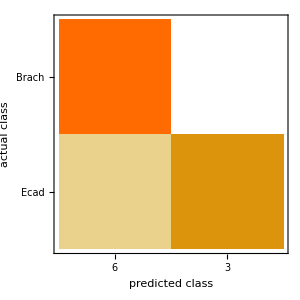

```mathematica
ClassifierMeasurements[classifier,DeleteCases[testingData,<|__|>->"EB"],"ConfusionMatrixPlot"]
```